### Arg Color Plot

Plot the absolute value Abs[f[x]] of a complex-valued function f depending on a real variable x and fill the space between the plotted function and the x-axis with a color corresponding to the argument Arg[f[x]]. The saturation and brightness of the colors can be set using the options QSaturation and QBrightness.

QArgColorPlot[f[x],{x,x0,x1},opts] |  is used like the usual Plot command. It gives a two-dimensional plot of a complex-valued function f of a single real variable x in the range {x0,x1}. The plot shows the curve Abs[f] with area between the curve and the x-axis colored by Hue[Arg[f[x]]/(2 Pi)]. The default options of Plot are changed to Axes->{True,None}, Fame->True. Package: VQM`ArgColorPlot`
QListArgColorPlot[f,{x,x0,x1},opts] |  plots a Abs[f], where f is a list of complex numbers. The  points of the list Abs[f] are joined by a line. The area between the curve and the x-axis is colored at each point by Hue[Arg[f]/(2 Pi)]. Package: VQM`ArgColorPlot`
QCombinedPlot[{f[x],g[x]},{x,x0,x1},opts] |  works like QArgColorPlot with respect to f. The curve g is drawn in front of the QArgColorPlot of f. Package: VQM`ArgColorPlot`
QListCombinedPlot[{list,f[x]},{x,x0,x1},opts] |  works like QListArgColorPlot with respect to list. It is assumed that list represents the discretized values of a function defined on the interval [x0,x1]. The color list plot is then combined with an ordinary plot of f on the same scale and with the Ticks automatically adjusted. Package: VQM`ArgColorPlot`
QSpinorPlot[{func1,func2},{x,x0,x1},opts] |  provides a method to visualize C^2-valued functions (for example, spinor wavefunctions in quantum mechanics). The QSpinorPlot combines a QArgColorPlot of func1 with a QArgColorPlot of func2 (upside down, with less saturation) Both curves are plotted with the option QSquared->True (that is, a plot of the curve Abs[func]^2 is filled with a color describing the phase). In the background, a filled plot of Abs[func1]^2 + Abs[func2]^2 displays the corresponding density. Package: VQM`ArgColorPlot`
QListSpinorPlot[list,opts] |  visualizes a spinor-valued list of complex numbers. Each element of list is a C^-vector, that is, list = {{z11,z12},{z21,z22},...}. Alternatively, list = {list1,list2} with two lists of complex numbers, list1 giving the upper component of the spinor-valued wave function, and list2 giving the lower component. The lower component is plotted upside down with less saturation. See also the description of QSpinorPlot. Package: VQM`ArgColorPlot`
QSpinorCombinedPlot[{func1,func2},{x,x0,x1},opts] |  combines a QSpinorPlot of func1 with an ordinary Plot of a real-valued function func2. See the description of QCombinedPlot and of QSpinorPlot. Package: VQM`ArgColorPlot`
QListSpinorCombinedPlot[{list,f[x]},{x,x0,x1},opts] |  combines a QListSpinorPlot of list1 with an ordinary Plot  of a real-valued function f. See the description of QListCombinedPlot and of QListSpinorPlot. Package: VQM`ArgColorPlot`
QNiceTicks[xmin,xmax,dx] |  provides a list of nice positions for use in the Ticks or FrameTicks option in a ListPlot, where it is assumed that the list of values ranges between xmin and xmax in steps dx. Package: VQM`ArgColorPlot`

This loads the package

```mathematica
Needs["VQM`ArgColorPlot`"]
```

This is an example

```mathematica
msgonindet=Head[General::"indet"]=!=$Off;
Off[Arg::"indet"];
```

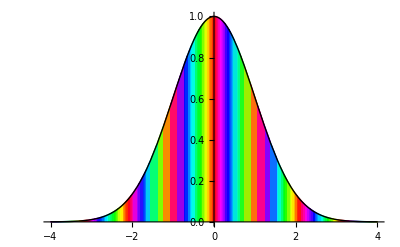

```mathematica
QArgColorPlot[ⅇ^(-ⅈ 6 x-x^2/2),{x,-4,4}]
```

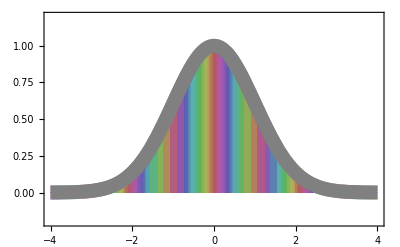

```mathematica
QArgColorPlot[ⅇ^(-ⅈ 6 x-x^2/2),{x,-4,4},PlotStyle->{Thickness[0.025],GrayLevel[0.5]},QSaturation->0.5,QBrightness->0.7,PlotRange->{-0.2,1.2},Frame->True,Axes->{True,False}]
```

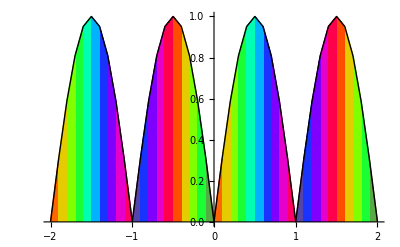

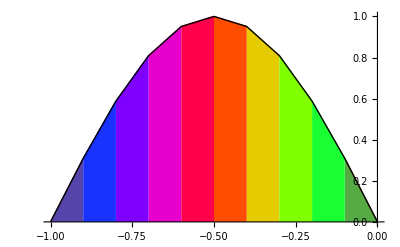

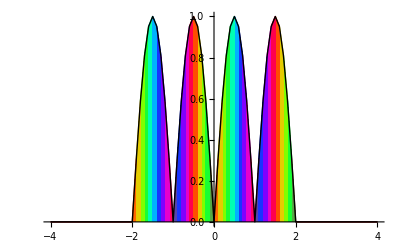

```mathematica
mytab=Table[Sin[π x] ⅇ^(2 ⅈ π x),{x,-2,2,0.1}];
QListArgColorPlot[mytab,Axes->True,QHorizontalRange->{-2,2}]
QListArgColorPlot[mytab,Axes->True,QHorizontalRange->{{-2,2},{-1,0}}]
QListArgColorPlot[mytab,Axes->True,QHorizontalRange->{{-2,2},{-4,4}}]
```

```mathematica
QCombinedPlot[{Sin[π x],Sin[π x]},{x,-4,3}]
```

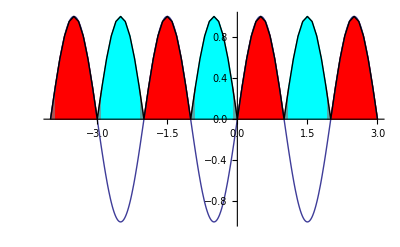

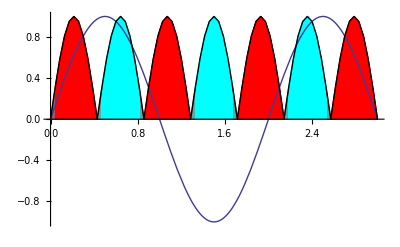

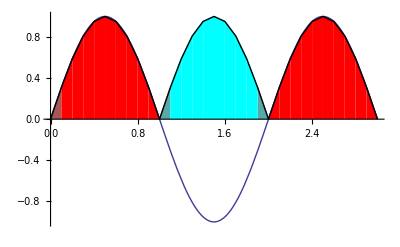

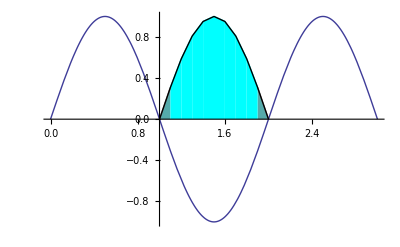

```mathematica
mytab=Table[Sin[π x],{x,-4,3,0.1}];
QListCombinedPlot[{mytab,Sin[π x]},{x,-4,3}]
QListCombinedPlot[{mytab,Sin[π x]},{x,0,3}]
QListCombinedPlot[{mytab,Sin[π x]},{x,0,3},QHorizontalRange->{-4,3}]
QListCombinedPlot[{mytab,Sin[π x]},{x,0,3},QHorizontalRange->{{-4,3},{1,2}}]
```

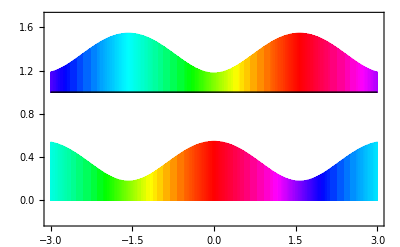

```mathematica
Show[QArgColorPlot[Sin[x+ⅈ],{x,-3,3},QBottomLine->1,Epilog->Line[{{-3,1},{3,1}}]],QArgColorPlot[Cos[x+ⅈ]-ⅇ^(ⅈ Arg[Cos[x+ⅈ]]),{x,-3,3}],PlotRange->{-0.2,1.7},Frame->True]
```

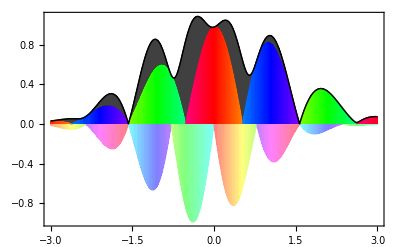

```mathematica
spinorfunction[x_]:={Cos[3 x] ⅇ^(-1/3 (x-1/4)^2+ⅈ x),Sin[4 x] ⅇ^(-1/2 (x+1/4)^2+2 ⅈ x)}
QSpinorPlot[Evaluate[spinorfunction[x]],{x,-3.,3.},PlotRange->All,Frame->True,Axes->{True,False}]
```

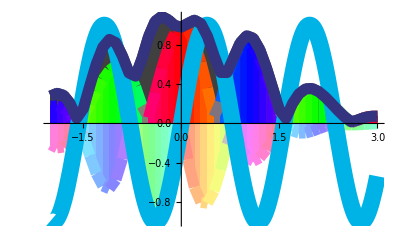

```mathematica
spinorlist=Table[{x,spinorfunction[x]},{x,-3,3,0.1}];
QListSpinorCombinedPlot[{spinorlist,Sin[4 x]},{x,-2,3},PlotRange->All,QCurveStyle->{RGBColor[0,0.7,0.9],Thickness[0.03]},PlotStyle->{RGBColor[0.2,0.2,0.5],Thickness[0.02]}]
```

```mathematica
If[msgonindet,On[Arg::"indet"]];
```